# OrderlessCombinations

OrderlessCombinations[list,n]
gives all possible orderless sets comprised of the elements of list up to length n. 
   OrderlessCombinations[list,{n}]
gives sets of exactly length n. 
   OrderlessCombinations[list,{n,m}]
gives sets containing between n and m elements. 
   OrderlessCombinations[list,{n,m,t}]
uses step t. 
   OrderlessCombinations[list,{i_1,i_2,…}]
uses the successive values i_1, i_2, ….

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

"XXXX" ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

Wolfram MathWorld—Multichoose

Wikipedia—Multiset

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`CombinatoricsPaclet`"]
```

## Basic Examples | More Examples ⊳

There are nine possible orderless sets of up to two elements chosen from three possible elements:

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

If one wishes to count the number of ways to distribute seven indistinguishable one dollar coins among Amber, Ben, and Curtis so that each of them receives at least one dollar, one may observe that distributions are essentially equivalent to tuples of three positive integers whose sum is 7. (Here the first entry in the tuple is the number of coins given to Amber, and so on.) Thus stars and bars theorem 1 applies, with n = 7 and k = 3, and there are (7-1
3-1)=15 ways to distribute the coins.

```mathematica
Length@OrderlessCombinations[{"Amber","Ben","Curtis"},{7}]
```

36

```mathematica
Length@OrderlessCombinations[{"Amber","Ben","Curtis"},7]
```

119

```mathematica
Multichoose[3,7]
```

36

```mathematica
Multichoose[5,9]
```

715

```mathematica
Multichoose[9,5]
```

1287

```mathematica
ThirtyFoldWay[3,7]
```

{{1,181440,0,75600,322560},{1,181440,2187,1,1779813},{1,0,36,15,64},{1,0,32760,12600,37633},{1,0,365,301,877},{1,0,8,4,15}}

```mathematica
ThirtyFoldWay[7,3]
```

{{1,504,210,0,24},{1,504,343,1,0},{1,35,84,0,4},{1,1,13,0,13},{1,1,5,0,5},{1,1,3,0,3}}

```mathematica
Sum[Multichoose[3,n],{n,7}]
```

119

```mathematica
Multichoose[4,5]
```

56

A recipe calls for 5 pinches of spice out of 9 spices. You have 9 spices in your cupboard. You select 5 spices. How many ways can you make a recipe with five spices?

```mathematica
Multichoose[9,5]
```

1287

You have 4 spices in your cupboard. You have cumin, coriander, turmeric, and paprika. You select 5 spices. How many ways can you make a recipe with five spices?

```mathematica
Dataset[OrderlessCombinations[{"cumin","coriander","turmeric","paprika"},{5}],DatasetTheme->"Web"]
```

```mathematica
Length[OrderlessCombinations[{"cumin","coriander","turmeric","paprika"},{5}]]
```

56

Use multichoose to calculate the result directly.

```mathematica
Multichoose[4,5]
```

56

Here's a harder problem where it will not work to list all the orderless combinations that we can compute with Multichoose.

We have some construction materials:

```mathematica
EntityValue[EntityClass["ConstructionMaterial",All],"Entities"]
```

{adobe,aluminum,ashlar,Bargate stone,basalt,Bath stone,bluestone,boulders,brick,bronze,calciferous sandstone,Carrara marble,cast iron,cement,ceramic,chalk,clay,clunch,cob,cobblestone,Collyweston stone slate,concrete,conglomerate,copper,Cotswold stone,diorite,dolomite,earth,expanded clay aggregate,fieldstone,flint,glass,gold,granite,gravel,gritstone,hamstone,iron,ironstone,Jerusalem stone,laterite,lead,lime,lime mortar,limestone,London stock brick,magnesian limestone,marble,marlstone,mortar,mosaic,mud,mudstone,New Red Sandstone,Old Red Sandstone,plaster,Portland stone,precast cladding,puddingstone,rag-stone,rammed earth,reinforced concrete,rock,roof shingle,roughcast,rubble,rubble masonry,Ryukyuan limestone,sand,sandstone,septaria,shale,siltstone,slate,soapstone,stained glass,steel,stucco,Sydney sandstone,terracotta,thatching,tile,timber,tin,travertine,tufa,tuff,Westmorland slate,whinstone,white sandstone,wood,wrought iron}

How many ways can we

```mathematica
FindClusters[EntityValue[EntityClass["ConstructionMaterial",All],"Entities"]]
```

Interpreter::nvldtype: ConstructionMaterial is not a known type for Interpreter.

General::stop: Further output of Interpreter::nvldtype will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Lookup[#1,#2,0]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1|>,<|«1»|>},{Transpose[«69»[Interpreter[Constr…aterial][«1»],«1»]]}}]; dimensions are 2 and 1.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[MapThread[Lookup[#1,#2,0]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1|>,<|Transpose[«1»]→1|>},{Transpose[«69»[«1»,«1»]]}}],«1»].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[1./(MachineLearning`file88Vector`PackagePrivate`vectorLength[Transpose[MapThread[Lookup[«3»]&,{«1»}],«1»]]),{MachineLearning`file88Vector`PackagePrivate`vectorLength[Transpose[MapThread[Lookup[«1»,«1»,0]&,«1»],«1»]]}].

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Lookup[#1,#2,0.]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1.|>,<|«1»|>},{Transpose[«69»[Interpreter[Cons…erial][«1»],«1»]]}}]; dimensions are 2 and 1.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Transpose::permspec: Invalid permutation specification found at position 2 in Transpose[MapThread[Lookup[#1,#2,0.]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1.|>,<|«1»|>},{Transpose[«69»[«11»[C…l][«1»],«1»]]}}],«1»].

General::stop: Further output of Transpose::permspec will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[1./(MachineLearning`file88Vector`PackagePrivate`vectorLength[Transpose[MapThread[Lookup[«3»]&,{«1»}],«1»]]),{MachineLearning`file88Vector`PackagePrivate`vectorLength[Transpose[MapThread[«1»&,{{<|«1»|>,«1»},«1»}],«1»]]}].

RandomChoice::lrwl: The items for choice Transpose[MapThread[Lookup[#1,#2,0.]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1.|>,<|«1»|>},{Transpose[«69»[«11»[C…l][«1»],«1»]]}}],«1»] should be a non-empty list or a rule weights -> choices.

Set::shape: Lists {MachineLearning`file49ClusterClassify`PackagePrivate`p1$39359,MachineLearning`file49ClusterClassify`PackagePrivate`p2$39359} and RandomChoice[Transpose[MapThread[Lookup[#1,#2,0.]&,{{<|Transpose[MachineLearning`file76EntityDateLocation`PackagePrivate`getProperties[Interpreter[ConstructionMaterial][{adobe}],{Name}]]→1.|>,<|Transpose[«1»]→1.|>},{«1»}}],«1»],2] are not the same shape.

FindClusters::wrgdist: The chosen distance function HammingDistance cannot be computed on the data. Try to specify a different distance.

FindClusters[{adobe,aluminum,ashlar,Bargate stone,basalt,Bath stone,bluestone,boulders,brick,bronze,calciferous sandstone,Carrara marble,cast iron,cement,ceramic,chalk,clay,clunch,cob,cobblestone,Collyweston stone slate,concrete,conglomerate,copper,Cotswold stone,diorite,dolomite,earth,expanded clay aggregate,fieldstone,flint,glass,gold,granite,gravel,gritstone,hamstone,iron,ironstone,Jerusalem stone,laterite,lead,lime,lime mortar,limestone,London stock brick,magnesian limestone,marble,marlstone,mortar,mosaic,mud,mudstone,New Red Sandstone,Old Red Sandstone,plaster,Portland stone,precast cladding,puddingstone,rag-stone,rammed earth,reinforced concrete,rock,roof shingle,roughcast,rubble,rubble masonry,Ryukyuan limestone,sand,sandstone,septaria,shale,siltstone,slate,soapstone,stained glass,steel,stucco,Sydney sandstone,terracotta,thatching,tile,timber,tin,travertine,tufa,tuff,Westmorland slate,whinstone,white sandstone,wood,wrought iron}]

```mathematica
CommonName/@EntityValue[EntityClass["ConstructionMaterial",All],"Entities"]
```

{adobe,aluminum,ashlar,Bargate stone,basalt,Bath stone,bluestone,boulders,brick,bronze,calciferous sandstone,Carrara marble,cast iron,cement,ceramic,chalk,clay,clunch,cob,cobblestone,Collyweston stone slate,concrete,conglomerate,copper,Cotswold stone,diorite,dolomite,earth,expanded clay aggregate,fieldstone,flint,glass,gold,granite,gravel,gritstone,hamstone,iron,ironstone,Jerusalem stone,laterite,lead,lime,lime mortar,limestone,London stock brick,magnesian limestone,marble,marlstone,mortar,mosaic,mud,mudstone,New Red Sandstone,Old Red Sandstone,plaster,Portland stone,precast cladding,puddingstone,rag-stone,rammed earth,reinforced concrete,rock,roof shingle,roughcast,rubble,rubble masonry,Ryukyuan limestone,sand,sandstone,septaria,shale,siltstone,slate,soapstone,stained glass,steel,stucco,Sydney sandstone,terracotta,thatching,tile,timber,tin,travertine,tufa,tuff,Westmorland slate,whinstone,white sandstone,wood,wrought iron}

```mathematica
FindClusters[CommonName/@EntityValue[EntityClass["ConstructionMaterial",All],"Entities"]]
```

{{adobe,aluminum,ashlar,Bargate stone,basalt,Bath stone,bluestone,boulders,bronze,calciferous sandstone,Carrara marble,cast iron,cement,ceramic,clay,clunch,cob,cobblestone,Collyweston stone slate,concrete,conglomerate,copper,Cotswold stone,diorite,dolomite,earth,expanded clay aggregate,fieldstone,flint,glass,gold,granite,gravel,gritstone,hamstone,iron,ironstone,Jerusalem stone,laterite,lead,lime,lime mortar,limestone,London stock brick,magnesian limestone,marble,marlstone,mortar,mosaic,mud,mudstone,New Red Sandstone,Old Red Sandstone,plaster,Portland stone,precast cladding,puddingstone,rag-stone,rammed earth,reinforced concrete,roof shingle,roughcast,rubble,rubble masonry,Ryukyuan limestone,sand,sandstone,septaria,shale,siltstone,slate,soapstone,stained glass,steel,stucco,Sydney sandstone,terracotta,thatching,tile,timber,tin,travertine,Westmorland slate,whinstone,white sandstone,wood,wrought iron},{brick,chalk,rock},{tufa,tuff}}

```mathematica
FindClusters[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

{{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},{RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}]},{RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}]},{RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}]},{RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}]}}

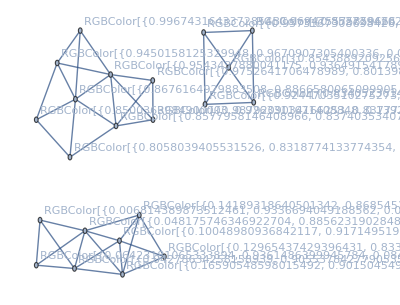

```mathematica
NearestNeighborGraph[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]},3,VertexLabels->All]
```

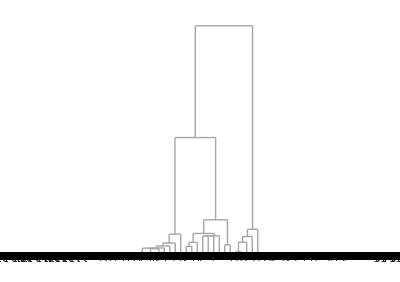

```mathematica
Dendrogram[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

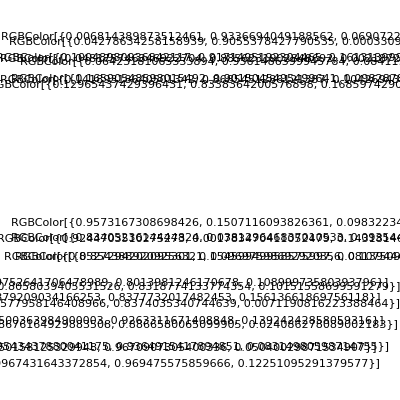

```mathematica
FeatureSpacePlot[{RGBColor[{0.048175746346922704, 0.8856231902848692, 0.002187262571789972}],RGBColor[{0.9543437880041175, 0.9364915417894851, 0.08314980598714755}],RGBColor[{0.8527294202095301, 0.15459949958575997, 0.08139444813034824}],RGBColor[{0.12965437429396431, 0.8338364200576898, 0.16859742903104202}],RGBColor[{0.14189318640501342, 0.8685451286121387, 0.10426943556314977}],RGBColor[{0.9244703510275273, 0.001783470411052479, 0.14318146272477922}],RGBColor[{0.8340523614444824, 0.038129646837010533, 0.09354464468116397}],RGBColor[{0.06423181065333894, 0.9361486399945784, 0.08411970647251821}],RGBColor[{0.8676164929883508, 0.8866580065099905, 0.024086278089002183}],RGBColor[{0.8577958146408966, 0.8374035340744639, 0.0071190816223388464}],RGBColor[{0.9967431643372854, 0.969475575859666, 0.12251095291379577}],RGBColor[{0.8543889209256321, 0.09697598692920356, 0.10750903324099509}],RGBColor[{0.8500363984900003, 0.9263311671408848, 0.13924242858059316}],RGBColor[{0.9879209034166253, 0.8377732017482453, 0.15613661869756118}],RGBColor[{0.9573167308698426, 0.1507116093826361, 0.09832234398916928}],RGBColor[{0.04278634258158939, 0.9055378427790535, 0.0003309996431954121}],RGBColor[{0.8058039405531526, 0.8318774133774354, 0.10151558699591279}],RGBColor[{0.006814389873512461, 0.9336694049188562, 0.06907220235176909}],RGBColor[{0.9450158125329948, 0.9670907305400336, 0.05040029871534907}],RGBColor[{0.9752641706478989, 0.8013981246170678, 0.10899973580393796}],RGBColor[{0.16590548598015492, 0.9015045495499641, 0.09828783196817376}],RGBColor[{0.10048980936842117, 0.9171495192304465, 0.16131399976146749}]}]
```

### Applications

A company makes 92 different construction materials, listed below. The customer needs a row of 403 buildings and edifices. How many different construction material combinations are available to the customer:

```mathematica
constructionMaterials=EntityValue[EntityClass["ConstructionMaterial",All],"Entities"]
```

{adobe,aluminum,ashlar,Bargate stone,basalt,Bath stone,bluestone,boulders,brick,bronze,calciferous sandstone,Carrara marble,cast iron,cement,ceramic,chalk,clay,clunch,cob,cobblestone,Collyweston stone slate,concrete,conglomerate,copper,Cotswold stone,diorite,dolomite,earth,expanded clay aggregate,fieldstone,flint,glass,gold,granite,gravel,gritstone,hamstone,iron,ironstone,Jerusalem stone,laterite,lead,lime,lime mortar,limestone,London stock brick,magnesian limestone,marble,marlstone,mortar,mosaic,mud,mudstone,New Red Sandstone,Old Red Sandstone,plaster,Portland stone,precast cladding,puddingstone,rag-stone,rammed earth,reinforced concrete,rock,roof shingle,roughcast,rubble,rubble masonry,Ryukyuan limestone,sand,sandstone,septaria,shale,siltstone,slate,soapstone,stained glass,steel,stucco,Sydney sandstone,terracotta,thatching,tile,timber,tin,travertine,tufa,tuff,Westmorland slate,whinstone,white sandstone,wood,wrought iron}

```mathematica
Length[constructionMaterials]
```

92

We compute ((92
403)) to get the answer.

```mathematica
Multichoose[92,403]
```

143086462343588913840387823397927962886765822717425132730651157932488959345072116876157136357586186616

As a smaller example, say we have 6 construction materials and we need to select 10. How many possible ways are there?

```mathematica
randomSample=RandomSample[constructionMaterials,6]
```

{rubble,siltstone,ashlar,granite,puddingstone,wrought iron}

```mathematica
EchoTiming[Length[OrderlessCombinations[randomSample,{10}]]]
```

0.0715414

3003

This fits with Multichoose:

```mathematica
EchoTiming[Multichoose[6,10]]
```

9.5×10^-6

3003

Now we have 7 construction materials and need 25. How many ways are there?

```mathematica
randomSample=RandomSample[constructionMaterials,7]
```

{marble,tufa,mortar,gritstone,puddingstone,travertine,precast cladding}

```mathematica
EchoTiming[Length[OrderlessCombinations[randomSample,{25}]]]
```

25.6618

736281

We can compute the answer with Multichoose faster:

```mathematica
EchoTiming[Multichoose[7,25]]
```

8.6×10^-6

736281

A recipe calls for 5 pinches of spice out of 9 spices. You have 9 spices in your cupboard. You select 5 spices. How many ways can you make a recipe with five spices?

```mathematica
Multichoose[9,5]
```

1287

```mathematica
spices={"cumin","coriander","paprika","turmeric","black-pepper"};
```

```mathematica
Length[OrderlessCombinations[spices,{9}]]
```

715

```mathematica
Length[OrderlessCombinations[Range[9],{5}]]
```

1287

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/CombinatoricsPaclet

PeterBurbery`CombinatoricsPaclet`

PeterBurbery/CombinatoricsPaclet/ref/OrderlessCombinations

### Keywords

### Syntax Templates